Last modified on: Wednesday, July 11, 2018 at 2:35

Author Info

Anjali Raj

Jonathan Gorard

Indian Institute of Technology Roorkee

Poster Session Content

Algebraic Computations on Tropical Semi-Rings

To implement and investigate arithmetic and matrix algebra over tropical semi-rings (min-plus and max-plus algebra) using Wolfram Language and explore some of its applications.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

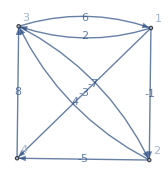
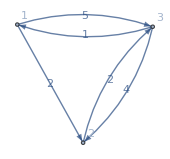
-Graphics--Graphics--Graphics-

I started with implementing the basic functions to compute linear algebra operations and then extended it for computing the general matrix operations over tropical semi-rings. 
Computational infeasibility (NP Hardness) of solving systems of linear equations in tropical algebra makes it a good candidate for key generation in an encryption algorithm. So I implemented the key generation function for cryptographic applications. Apart from that, I implemented an efficient method that finds shortest path between two vertices in at most m steps for a given graph.  
The package I have developed for tropical semi-rings can be used for further exploration of the applications of tropical algebra.

Since tropical algebra itself is a new branch of mathematics, much of its applications are not known to us. Due to the efficiency of matrix multiplication in tropical algebra, some interesting results for graph theory can be derived and possibly a deeper connection between graph theory and tropical algebra can be established. 
Other than graph theory applications, NP Hardness of solving systems of linear equations can be used as the basis of creating much stronger cryptosystem than already existing. 
Now that we already have a package to implement tropical algebra, it will be much easier to investigate its other possible applications.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Shortest path between a pair of vertices in a graph

Given a directed graph G = {V, E} of n vertices and a transition cost matrix C ∈ ℝ_nxn where C_ij = weight of the edge (i, j). 
In tropical algebra, (C^m)_ijis the minimum cost of moving from vertex i to vertex j in at most m steps. 
Note: If all the elements in the cost matrix are positive, then C^m = C^2 for m ≥ 2, since any trip of size 3 or more steps contains a circuit.

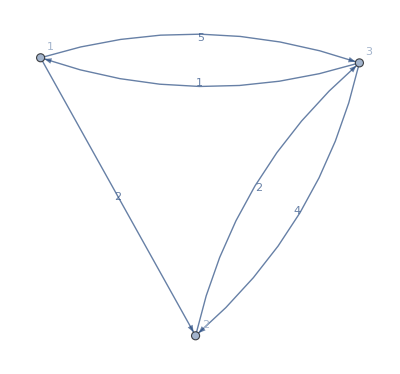

TropicalMatrixSquare[c]//MatrixForm
(0 | 2 | 4
3 | 0 | 2
1 | 3 | 0)

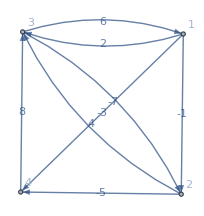

TropicalMatrixExp[c, 10]//MatrixForm
(-37 | -50 | -44 | -53
-35 | -48 | -42 | -51
-40 | -53 | -48 | -57
-31 | -44 | -38 | -47)

Key generation for cryptographic applications

Given the public key matrices A and B, the sender and receiver chooses two random polynomials and send their product to each other.

p = TropicalMatrixTimes[p1A, p2B];
q = TropicalMatrixTimes[q1A, q2B];

keyA = TropicalMatrixTimes[TropicalMatrixTimes[p1A, q], p2B]
keyB = TropicalMatrixTimes[TropicalMatrixTimes[q1A, p], q2B]

{{-329800608957,-329391125900,-329912924534,-328275472711,-328792508141,-331493856596,-332704704247,-329660812825,-330660684702,-326413843447},{-337552897327,-337143414270,-337665212904,-336027761081,-336544796511,-339246144966,-340456992617,-337413101195,-338412973072,-334166131817},{-339196077746,-338786594689,-339308393323,-337670941500,-338187976930,-340889325385,-342100173036,-339056281614,-340056153491,-335809312236},{-338200658907,-337791175850,-338312974484,-336675522661,-337192558091,-339893906546,-341104754197,-338060862775,-339060734652,-334813893397},{-334774149592,-334364666535,-334886465169,-333249013346,-333766048776,-336467397231,-337678244882,-334634353460,-335634225337,-331387384082},{-334936465362,-334526982305,-335048780939,-333411329116,-333928364546,-336629713001,-337840560652,-334796669230,-335796541107,-331549699852},{-336925332116,-336515849059,-337037647693,-335400195870,-335917231300,-338618579755,-339829427406,-336785535984,-337785407861,-333538566606},{-333818335497,-333408852440,-333930651074,-332293199251,-332810234681,-335511583136,-336722430787,-333678539365,-334678411242,-330431569987},{-339524306602,-339114823545,-339636622179,-337999170356,-338516205786,-341217554241,-342428401892,-339384510470,-340384382347,-336137541092},{-336462389908,-336052906851,-336574705485,-334937253662,-335454289092,-338155637547,-339366485198,-336322593776,-337322465653,-333075624398}}

{{-329800608957,-329391125900,-329912924534,-328275472711,-328792508141,-331493856596,-332704704247,-329660812825,-330660684702,-326413843447},{-337552897327,-337143414270,-337665212904,-336027761081,-336544796511,-339246144966,-340456992617,-337413101195,-338412973072,-334166131817},{-339196077746,-338786594689,-339308393323,-337670941500,-338187976930,-340889325385,-342100173036,-339056281614,-340056153491,-335809312236},{-338200658907,-337791175850,-338312974484,-336675522661,-337192558091,-339893906546,-341104754197,-338060862775,-339060734652,-334813893397},{-334774149592,-334364666535,-334886465169,-333249013346,-333766048776,-336467397231,-337678244882,-334634353460,-335634225337,-331387384082},{-334936465362,-334526982305,-335048780939,-333411329116,-333928364546,-336629713001,-337840560652,-334796669230,-335796541107,-331549699852},{-336925332116,-336515849059,-337037647693,-335400195870,-335917231300,-338618579755,-339829427406,-336785535984,-337785407861,-333538566606},{-333818335497,-333408852440,-333930651074,-332293199251,-332810234681,-335511583136,-336722430787,-333678539365,-334678411242,-330431569987},{-339524306602,-339114823545,-339636622179,-337999170356,-338516205786,-341217554241,-342428401892,-339384510470,-340384382347,-336137541092},{-336462389908,-336052906851,-336574705485,-334937253662,-335454289092,-338155637547,-339366485198,-336322593776,-337322465653,-333075624398}}

keyA == keyB
True

{{-329800608957,-329391125900,-329912924534,-328275472711,-328792508141,-331493856596,-332704704247,-329660812825,-330660684702,-326413843447},{-337552897327,-337143414270,-337665212904,-336027761081,-336544796511,-339246144966,-340456992617,-337413101195,-338412973072,-334166131817},{-339196077746,-338786594689,-339308393323,-337670941500,-338187976930,-340889325385,-342100173036,-339056281614,-340056153491,-335809312236},{-338200658907,-337791175850,-338312974484,-336675522661,-337192558091,-339893906546,-341104754197,-338060862775,-339060734652,-334813893397},{-334774149592,-334364666535,-334886465169,-333249013346,-333766048776,-336467397231,-337678244882,-334634353460,-335634225337,-331387384082},{-334936465362,-334526982305,-335048780939,-333411329116,-333928364546,-336629713001,-337840560652,-334796669230,-335796541107,-331549699852},{-336925332116,-336515849059,-337037647693,-335400195870,-335917231300,-338618579755,-339829427406,-336785535984,-337785407861,-333538566606},{-333818335497,-333408852440,-333930651074,-332293199251,-332810234681,-335511583136,-336722430787,-333678539365,-334678411242,-330431569987},{-339524306602,-339114823545,-339636622179,-337999170356,-338516205786,-341217554241,-342428401892,-339384510470,-340384382347,-336137541092},{-336462389908,-336052906851,-336574705485,-334937253662,-335454289092,-338155637547,-339366485198,-336322593776,-337322465653,-333075624398}}

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

In the package for tropical algebra, I have implemented the fundamental functions (addition and multiplication) for numbers and lists. Some of the functions defined are trivial which includes identity matrix, transpose of a matrix and whether a given list is containing the same constant as all its elements.
 
For simplification of dealing tropical polynomials, I have implemented functions for exponentiation for numbers and matrices, computing the value of polynomials for a given number or a matrix and polynomial multiplication
For implementing matrix algebra, there are functions like determinant, singularQ, tropical rank, adjoint, pseudo inverse, eigenvalue data, eigenvalue and eigenvector in the package. Since  the only invertible matrices in tropical algebra are diagonal matrices, permutation matrices and their products, only pseudo inverse of the matrices has been implemented in the package. 

The basic functions required for implementing tropical algebra are all defined in the package.

#### Code

https://github.com/RajAnjali/Summer2018Starter-master

#### Conclusions in Detail

Using the package for tropical algebra, I have implemented an key generation algorithm which generates an encryption key of size 10^30 if the proper parameters for the variables are considered. To break the cryptosystem based on this key, one has to solve a system of tropical polynomials which is proved to be an NP hard problem. Infeasibility of such an computation makes this cryptosystem much more secure and invulnerable to the known linear attacks.

Another interesting property of matrix multiplication in tropical algebra is that if the elements in the matrix representation of a graph are non negative, then the square of that matrix gives the shortest path between all the pair of vertices. If the matrix has negative elements, then nth power of the matrix gives the shortest path between the pairs of vertices in at most n steps.

#### Future Directions

The min-plus algebra comprises one half of a field of tropical mathematics. All the functions in the package are defined for min-plus algebra. An analog of min-plus algebra can be implemented very easily for max plus algebra to complete the entire tropical algebra package.  
Tropical algebra is an integral part of geometric combinatorics and algebraic geometry. Tropical geometry is a branch of geometry manipulating with certain piecewise-linear objects that take over the role of classical algebraic varieties. Tropical algebra can hence be used to understand discrete event dynamic systems (DEDS). 
With the package developed for the tropical algebra, implementation for such systems will become much easier.

#### Background Info Links/References

```mathematica
https://scarab.bates.edu/cgi/viewcontent.cgi?article=1119&context=honorstheses
https://arxiv.org/pdf/math/0505458.pdf
https://eprint.iacr.org/2013/012.pdf
http://people.reed.edu/~davidp/homepage/students/borman.pdf
https://www.math.utah.edu/mathcircle/notes/MathCircleIv2.pdf
http://library.msri.org/books/Book52/files/13dev.pdf
```

#### Keywords

Provide keywords as items

Tropical algebra

Tropical semi-rings

Public key exchange

Cryptography

Shortest path in a graph